```mathematica
ClearAll["Global`*"]
```

```mathematica
rb1=Import["D:\\Dropbox\\@Droplet\\DATA\\resolution test\\data\\rb-res-window-1.tiff"];
```

```mathematica
rb1data=N@ImageData[rb1,"Byte"];
```

```mathematica
peak=Max@rb1data;
{xc,yc}=First@Position[rb1data,peak];
```

```mathematica
xsize=50;ysize=50;
IMGDATA3=rb1data[[xc-xsize;;xc+xsize,yc-ysize;;yc+ysize]];
IMG3=Colorize[ImageAdjust@Image[IMGDATA3],ColorFunction->"Temperature"]
```

-Graphics-

```mathematica
DataFit=Partition[Flatten@Table[{x,y,IMGDATA3[[x,y]]},{x,1,2*xsize+1},{y,1,2*ysize+1}],3];
```

```mathematica
fit=FindFit[DataFit,c+a*If[x==xcen&&y==ycen,1,(2BesselJ[1,k √((x-xcen)^2+(y-ycen)^2)])^2/(((x-xcen)^2+(y-ycen)^2)k^2)],{{c,0},{a,peak},{k,0.1},{xcen,xsize},{ycen,ysize}},{x,y}]
```

{c→0.313425,a→159.149,k→0.388939,xcen→51.3849,ycen→50.7167}

```mathematica
Show[Plot3D[c+a*If[x==xcen&&y==ycen,1,(2BesselJ[1,k √((x-xcen)^2+(y-ycen)^2)])^2/(((x-xcen)^2+(y-ycen)^2)k^2)]/.fit,{x,0,100},{y,0,100},PlotRange->All,PlotPoints->50],ListPointPlot3D[DataFit,PlotStyle->Directive[PointSize[Medium],Red]]]
```

-Graphics3D-

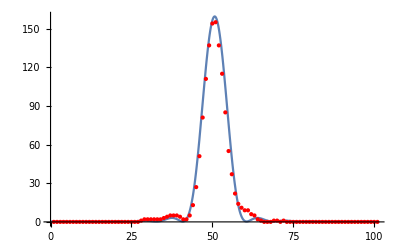

```mathematica
Show[Plot[c+a*If[x==xcen&&y==ycen,1,(2BesselJ[1,k √((x-xcen)^2+(y-ycen)^2)])^2/(((x-xcen)^2+(y-ycen)^2)k^2)]/.x->xcen/.fit,{y,0,100},PlotRange->All,PlotPoints->50],ListPlot[IMGDATA3[[50,All]],PlotStyle->Directive[PointSize[Medium],Red]]]
```

```mathematica
magnification=14.837;
pixelsize=3.45;
AiryRadius=1/k*π*1.22*pixelsize/magnification/.fit
```

2.2914

```mathematica
GaussainRMS=AiryRadius/3
```

0.7638